```mathematica
target[x_]:=2+3x+x^2
range={-10, 10, 0.01};
```

```mathematica
xVals=Range@@range;
funcFromVals[vals_][x_]:=Quiet[Interpolation[Transpose[{xVals, vals}],InterpolationOrder->1][x], {InterpolatingFunction::dmval, InterpolatingFunction::dprec}]
```

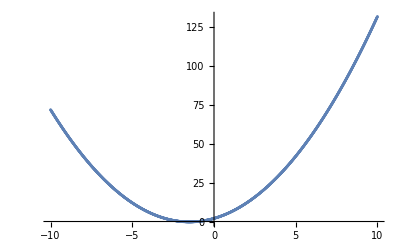

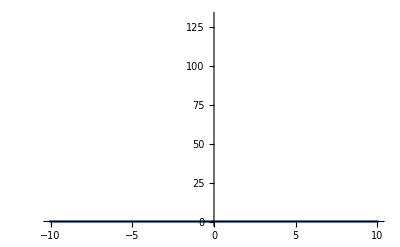

```mathematica
funcVals=target/@xVals;
approxVals=0*xVals;
plots={};

pRange=AbsoluteOptions[Plot[target[x], {x, range[[1]], range[[2]]}, ImageSize->Medium],PlotRange][[1,2]];

PlotVals[vals_]:=Show[{ListPlot[Transpose[{xVals, vals}], PlotRange->pRange], Plot[funcFromVals[vals][x], {x, range[[1]], range[[2]]}, PlotRange->pRange]}]
PlotVals[funcVals]
PlotVals[approxVals]
```

```mathematica
imax=10;jmax=5; (* j is how many steps to run in between plots, i is how many plots to generate *)

progress=PrintTemporary["0% Complete"];
Table[Table[
approxFunc=funcFromVals[approxVals];
nestedApproxVals=approxFunc[approxFunc[#]]&/@xVals;
deltaVals=funcVals-nestedApproxVals;
newApproxVals=approxVals+0.1*deltaVals;
approxVals=newApproxVals;
NotebookDelete[progress];
progress=PrintTemporary[ToString[Floor[100*(i*jmax+j)/((imax+1)*(jmax))]]<>"% Complete"];,{j, jmax}];
plots=AppendTo[plots,Plot[approxFunc[approxFunc[x]], {x, range[[1]], range[[2]]}, ImageSize->Small, PlotRange->pRange]];
, {i,imax}];
```

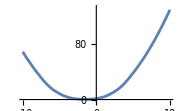
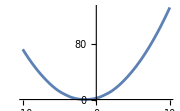
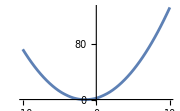
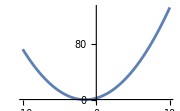
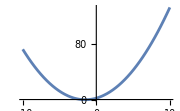
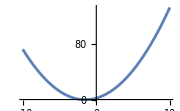
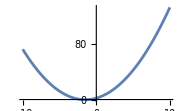
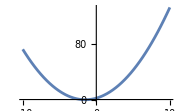

```mathematica
plots
```

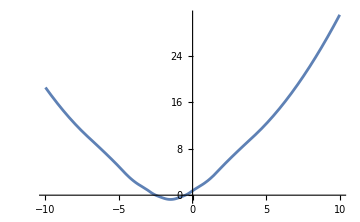
-Graphics-approx

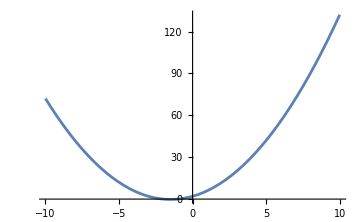
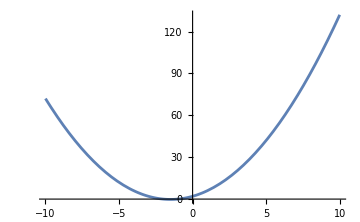
-Graphics-approx nested-Graphics-target

```mathematica
pSize=Medium;

pTarget=Plot[target[x], {x, range[[1]], range[[2]]}, ImageSize->pSize];
pApprox=Plot[approxFunc[x], {x, range[[1]], range[[2]]}, ImageSize->pSize];
pApproxNested=Plot[approxFunc[approxFunc[x]], {x, range[[1]], range[[2]]}, ImageSize->pSize, PlotRange->pRange];

Labeled[pApprox, "approx"]
Row[{Labeled[pApproxNested, "approx nested"], Labeled[pTarget, "target"]}]
```